```mathematica
h=Table[If[i==j,2λ,0],{i,10},{j,10}];
```

```mathematica
k=Table[If[i==j+1,-λ,0],{i,10},{j,10}];
```

```mathematica
m=Table[If[i==j-1,-λ,0],{i,10},{j,10}];
```

```mathematica
p=Table[h[[i,j]]+k[[i,j]]+m[[i,j]],{i,10},{j,10}];
```

```mathematica
P=MatrixForm[p]
```

(2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2)

```mathematica
λ=1;
```

```mathematica
eig=Eigenvalues[N[p]]
```

{3.91899,3.68251,3.30972,2.83083,2.28463,1.71537,1.16917,0.690279,0.317493,0.0810141}

```mathematica
121*eig/π^2
```

{48.0462,45.147,40.5767,34.7056,28.0092,21.0302,14.3339,8.46272,3.89242,0.993221}

```mathematica
h=Table[If[i==j,2λ,0],{i,100},{j,100}];
```

```mathematica
k=Table[If[i==j+1,-λ,0],{i,100},{j,100}];
```

```mathematica
m=Table[If[i==j-1,-λ,0],{i,100},{j,100}];
```

```mathematica
q=Table[h[[i,j]]+k[[i,j]]+m[[i,j]],{i,100},{j,100}];
```

```mathematica
λ=1;
```

```mathematica
eig=Eigenvalues[N[q]];
```

```mathematica
En=10201*eig/π^2;
```

```mathematica
TakeSmallest[En,5]
```

{0.999919,3.99871,8.99347,15.9794,24.9496}

```mathematica
eve10=Eigenvectors[N[p]];
```

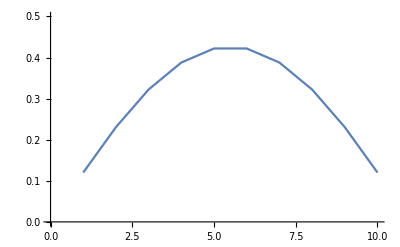

```mathematica
ListLinePlot[eve10[[10]],PlotRange->{0,.5}]
```

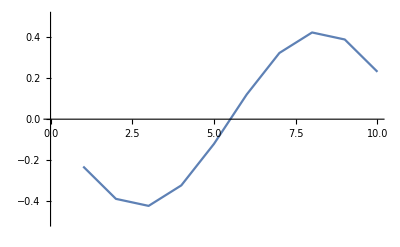

```mathematica
ListLinePlot[eve10[[9]],PlotRange->{-.5,.5}]
```

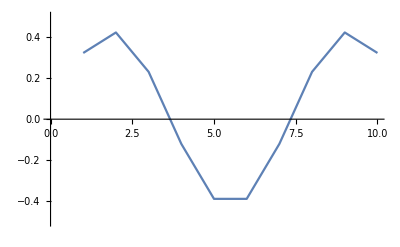

```mathematica
ListLinePlot[eve10[[8]],PlotRange->{-.5,.5}]
```

```mathematica
eve100=Eigenvectors[N[q]];
```

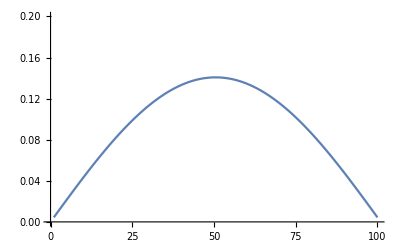

```mathematica
ListLinePlot[eve100[[100]],PlotRange->{0,.2}]
```

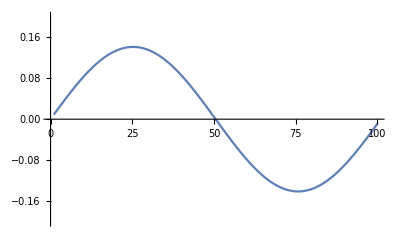

```mathematica
ListLinePlot[eve100[[99]],PlotRange->{-.2,.2}]
```

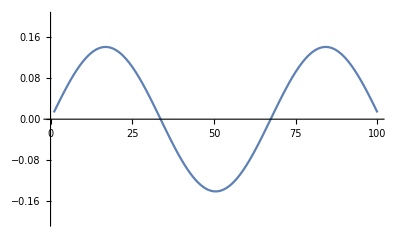

```mathematica
ListLinePlot[eve100[[98]],PlotRange->{-.2,.2}]
```